## Data for plots

```mathematica
<<MaTeX`
SetOptions[MaTeX,"FontSize"->12];
od=({{0, 1, 1, 1, 1, 1}, {0, 0, 1, 1, 1, 1}, {0, 0, 0, 1, 1, 1}, {0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0}});
total=100000;
```

```mathematica
(*ϵW=.055;
dataW={};
Monitor[
Do[
offdiagonal=od RandomReal[NormalDistribution[0,ϵW],{6,6}]+ⅈ od RandomReal[NormalDistribution[0,ϵW],{6,6}];
offdiagonal=offdiagonal+ConjugateTranspose[offdiagonal];

evals=Eigenvalues[DiagonalMatrix[{2/3,2/3,2/3,1/3,1/3,1/3}]+DiagonalMatrix[RandomReal[NormalDistribution[0,ϵW],{6}]]+offdiagonal];
AppendTo[dataW,evals⟦1⟧-1];

,{n,0,total}
]
,n]*)


(*ϵEPR=.083;
dataEPR={};
Monitor[
Do[
offdiagonal=od RandomReal[NormalDistribution[0,ϵEPR],{6,6}]+ⅈ od RandomReal[NormalDistribution[0,ϵEPR],{6,6}];
offdiagonal=offdiagonal+ConjugateTranspose[offdiagonal];

evals=Eigenvalues[DiagonalMatrix[{1,.5,.5,.5,.5,0}]+DiagonalMatrix[Join[RandomReal[NormalDistribution[0,ϵEPR],{5}],RandomReal[NormalDistribution[0,ϵEPR],{1}]//Abs]]+offdiagonal];
AppendTo[dataEPR,evals⟦2⟧-1];

,{n,0,total}
]
,n]*)
```

```mathematica
(*ϵGHZ=.037;
dataGHZ={};
Monitor[
Do[
offdiagonal=od RandomReal[NormalDistribution[0,ϵGHZ],{6,6}]+ⅈ od RandomReal[NormalDistribution[0,ϵGHZ],{6,6}];
offdiagonal=offdiagonal+ConjugateTranspose[offdiagonal];

evals=Eigenvalues[DiagonalMatrix[{.5,.5,.5,.5,.5,.5}]+DiagonalMatrix[RandomReal[NormalDistribution[0,ϵGHZ],{6}]]+offdiagonal];
AppendTo[dataGHZ,evals⟦1⟧+evals⟦3⟧+evals⟦2⟧-2];

,{n,0,total}
]
,n]*)
```

```mathematica
Export[NotebookDirectory[]<>"dataEPR.dat",dataEPR,"Table"];
Export[NotebookDirectory[]<>"dataW.dat",dataW,"Table"];
Export[NotebookDirectory[]<>"dataGHZ.dat",dataGHZ,"Table"];
```

```mathematica
dataEPR=Import[NotebookDirectory[]<>"dataEPR.dat"]//Flatten;
dataW=Import[NotebookDirectory[]<>"dataW.dat"]//Flatten;
dataGHZ=Import[NotebookDirectory[]<>"dataGHZ.dat"]//Flatten;
```

-0.151113

0.0494695

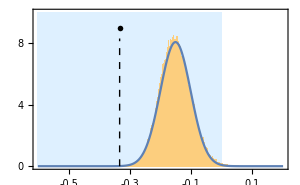

-0.00270413

```mathematica
μ2=Mean[dataW]
σ2=StandardDeviation[dataW]
line1=Line[{{-1/3,0},{-1/3,8.3}}];
P2=Show[Histogram[dataW,500,"PDF",Frame->True,FrameLabel->{MaTeX["F_{\\mathrm{EPR}}"],MaTeX["\\rho(F_{\\mathrm{EPR}})"]},Epilog->{{Directive[{Black,Dashed}],line1},{Text[MaTeX["\\mu=-"<>ToString[NumberForm[Abs[μ2],3]]],Scaled[{.81,.8}]],Text[MaTeX["\\sigma=+"<>ToString[NumberForm[σ2,2]]],Scaled[{.81,.67}]],Text[MaTeX["\\mathrm{theoretical}\\ \\mathrm{value}"],{-.333,9}]}},PlotRange->{{-.6,.2},{0,10}},BaseStyle->{FontFamily->"LM Roman 12",FontSize->12},ImageSize->300,PlotRangePadding->None,Prolog->{LightBlue,Rectangle[{-.6,0},{0,10}]},FrameTicks->{{{0,2,4,6,8,10},None},{{-.5,-.4,-.3,-.2,-.1,0,.1},None}}],Plot[PDF[NormalDistribution[μ2,σ2]][x],{x,-.6,.2},PlotRange->{{-.6,.2},{0,10}}]]
μ2+3σ2
```

-0.229331

0.0708253

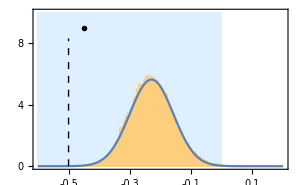

-0.0168551

```mathematica
line1=Line[{{-.5,0},{-.5,8.3}}];
μ1=Mean[dataEPR]
σ1=StandardDeviation[dataEPR]
P1=Show[Histogram[dataEPR,500,"PDF",Frame->True,FrameLabel->{MaTeX["F_{\\mathrm{Slater}}"],MaTeX["\\rho(F_{\\mathrm{Slater}})"]},Epilog->{Directive[{Black,Dashed}],line1,{Text[MaTeX["\\mu=-"<>ToString[NumberForm[Abs[μ1],3]]],Scaled[{.81,.8}]],Text[MaTeX["\\sigma=+"<>ToString[NumberForm[σ1,2]]],Scaled[{.81,.67}]],Text[MaTeX["\\mathrm{theoretical}\\ \\mathrm{value}"],{-.45,9}]}},PlotRange->{{-.6,.2},{0,10}},ImageSize->300,BaseStyle->{FontFamily->"LM Roman 12",FontSize->12},PlotRangePadding->None,Prolog->{LightBlue,Rectangle[{-.6,0},{0,10}]},FrameTicks->{{{0,2,4,6,8,10},None},{{-.5,-.4,-.3,-.2,-.1,0,.1},None}}],Plot[PDF[NormalDistribution[μ1,σ1]][x],{x,-.6,.2},PlotRange->{{-.6,.2},{0,10}}]]
μ1+3σ1
```

-0.189296

0.0605787

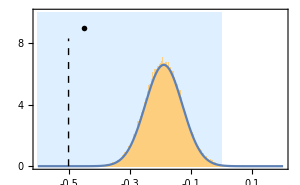

-0.00756047

```mathematica
μ3=Mean[dataGHZ]
σ3=StandardDeviation[dataGHZ]
line1=Line[{{-.5,0},{-.5,8.3}}];
P3=Show[Histogram[dataGHZ,500,"PDF",Frame->True,FrameLabel->{MaTeX["F_{\\mathrm{W}}"],MaTeX["\\rho(F_{\\mathrm{W}})"]},Epilog->{Directive[{Black,Dashed}],line1,{Text[MaTeX["\\mu=-"<>ToString[NumberForm[Abs[μ3],3]]],Scaled[{.81,.8}]],Text[MaTeX["\\sigma=+"<>ToString[NumberForm[σ3,2]]],Scaled[{.81,.67}]],Text[MaTeX["\\mathrm{theoretical}\\ \\mathrm{value}"],{-.45,9}]}},PlotRange->{{-.6,.2},{0,10}},BaseStyle->{FontFamily->"LM Roman 12",FontSize->12},ImageSize->300,PlotRangePadding->None,Prolog->{LightBlue,Rectangle[{-.6,0},{0,10}]},FrameTicks->{{{0,2,4,6,8,10},None},{{-.5,-.4,-.3,-.2,-.1,0,.1},None}}],Plot[{PDF[NormalDistribution[μ3,σ3]][x]},{x,-.6,.2},PlotRange->{{-.6,.2},{0,10}}]]
μ3+3σ3
```

## Plots for paper

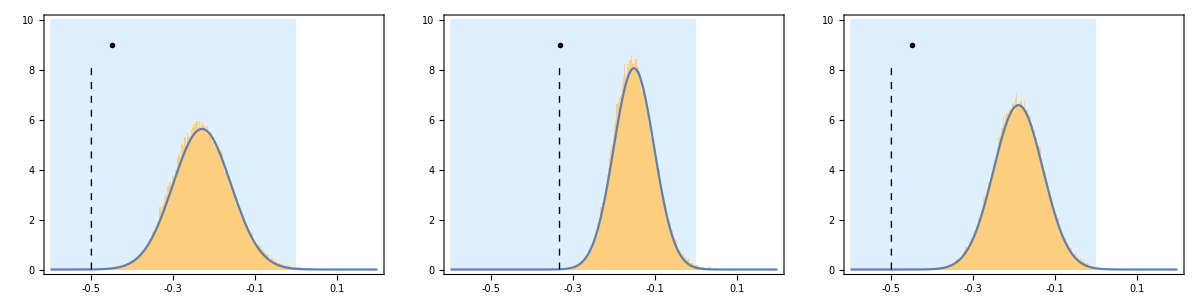

```mathematica
Plotf=Grid[{{P1,P2,P3}}]
Export[NotebookDirectory[]<>"ErrorFigure.pdf",Plotf];
```